```mathematica
Quit[];
```

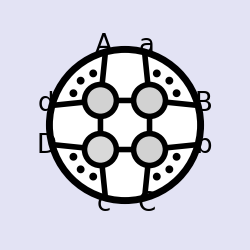
-Graphics-
One-Loop Amplitude Integrands
and Integrals in N=4 SYM
Jacob L. Bourjaily, 2013

```mathematica
<<loop_amplitudes.m
```

```mathematica
n=10;
(* fun *)
ab[___,j_,___,j_,___]:=0;
sortab={i_ab:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
sortdoubleab={i_doubleab:>Sort[i]Signature[i]/Signature[Sort[i]]};
sortcapinR=R[a__]:>R@@(Replace[List[a],cap[x_,y_]:>cap[ordercup@x,ordercup[y]],{0,Infinity}]);
Qlog[1]:=0;
Dmatrix[0]=0;
doubleab[___,j_,___,j_,___]:=0;
Dmatrix[ab[x__]y_]:=ab[x]Dmatrix[y];
FuseDmatrices:=Expand[#]//.{Dmatrix[i_]Dmatrix[j_]:>Dmatrix@Join[i,j]}&;
abelim={ab[x___,n+1,y___]:>ab[x,n,y]-e ab[x,B,y]};
abtre= ab[aa___,B,bb___]:>ab[aa,n-1,bb]-τ ab[aa,1,bb](ab[n-1,n,2,3]/ab[n,1,2,3])-e ab[aa,2,bb](ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1]);
capexpand = {ab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] ab[x, a, y] + ab[c, a] ab[x, b, y],
               ab[x___,cap1[{a_,b_},{c__},{d__}],y___]:>(-1)^Length[{y}](ab[x,y,a,c]ab[x,y,b,d]-ab[x,y,a,d]ab[x,y,b,c])};
shifexp={ab[x___,shift[y_,z_],w___]:>ab[x,y⟦1⟧,w]+z ab[x,y⟦2⟧,w]};
mom=RandomInteger[{-100,100},{20,4}];
mom1=Table[Binomial[n+i,i],{n,20},{i,0,3}];
neab[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom[[{x}]]];
neab1[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[mom1[[{x}]]];
todmatrix:=FuseDmatrices[#/.i_R:>(fromRform[n+1][i][[1,1]])Dmatrix[fromRform[n+1][i][[1,2]]]//.shifexp//.capexpand]&;
todmatrixn:=FuseDmatrices[#/.i_R:>(fromRform[n][i][[1,1]])Dmatrix[fromRform[n][i][[1,2]]]//.shifexp//.capexpand]&;
DmatrixEval[fermions__] :={Dmatrix[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1,4}],Dmatrix[i_]:>0};
order[exprn_,option_:1]:=If[option==0,exprn/.{ab[x__]:>Signature[{x}] ab@@Sort[{x}]},Block[{nGuess=Max[Join[{0},Flatten[Apply[List,Cases[exprn,_ab,{0,∞}],{1}]]]],consec,xLike},consec=Partition[Range[nGuess],2,1,1];xLike=Apply[If[Length[Range[#2,#3]]>Length[Range[#4,#1+nGuess]],{#3,#4,#1,#2},{##1}]&,Select[Flatten/@Subsets[consec,{2}],Length[#1∩#1]==4&],{1}];exprn/.{ab[x__]:>If[Length[{x}]==2,(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Signature[{x}] ab@@Sort[{x}]]&)[Select[consec,Length[{x}∩#1]==2&,1]],(If[Length[#1]==1,Signature[#1[[1]]] Signature[{x}] ab@@#1[[1]],Block[{xLikeLines=Select[consec,Length[#1∩{x}]==2&],boundaries},If[Length[xLikeLines]==0,Signature[{x}] ab@@Sort[{x}],boundaries=Complement[{x},xLikeLines[[1]]];If[Length[Range[boundaries[[2]],If[xLikeLines[[1,1]]<boundaries[[2]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[1]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[1]]]]>Length[Range[boundaries[[1]],If[xLikeLines[[1,1]]<boundaries[[1]],nGuess,0]+xLikeLines[[1,1]]]]+Length[Range[xLikeLines[[1,2]],If[boundaries[[2]]<xLikeLines[[1,2]],nGuess,0]+boundaries[[2]]]],boundaries=Reverse[boundaries];];-Signature[Join[boundaries,xLikeLines[[1]]]] Signature[{x}] ab@@RotateLeft[Join[boundaries,xLikeLines[[1]]]]]]]&)[Select[xLike,Length[#1∩{x}]==4&]]]}]];
twistorSchouten=#1//.{ab[a___,x_,b___,y_,c___] ab[d___,x_,e___,y_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,x,e,y,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}],ab[a___,x_,b___,y_,c___] ab[d___,y_,e___,x_,f___]:>Signature[Flatten[{x,y,Sort[{a,b,c}]}]] Signature[{a,x,b,y,c}] Signature[Flatten[{x,y,Sort[{d,e,f}]}]] Signature[{d,y,e,x,f}] ab@@Flatten[{x,y,Sort[{a,b,c}]}] ab@@Flatten[{x,y,Sort[{d,e,f}]}]}//.{ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,c_,b_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,b_,d_]:>ab[x,y,a,d] ab[x,y,c,b],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>ab[x,y,a,c] ab[x,y,b,d],ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]+ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>ab[x,y,a,d] ab[x,y,c,b],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,d_] ab[x_,y_,b_,c_]:>-ab[x,y,a,c] ab[x,y,b,d],-ab[x_,y_,a_,b_] ab[x_,y_,c_,d_]-ab[x_,y_,a_,c_] ab[x_,y_,d_,b_]:>-ab[x,y,a,d] ab[x,y,c,b]}&;
twistorSimplify[exprn_,orderQ_:0]:=If[Count[exprn,ab[x_,y_],∞]>0,Simplify[order[exprn]/.Apply[Rule,({#1,twistorSchouten[#1]}&)/@Cases[exprn,ab[x__] ab[y__]-ab[z__] ab[w__]|ab[x__] ab[y__]+ab[z__] ab[w__],{0,∞}],{1}]],order[FullSimplify[If[orderQ==1,order[FullSimplify[order[exprn,0],TransformationFunctions->{Automatic,twistorSchouten}],1],exprn],TransformationFunctions->{Automatic,twistorSchouten}],1]];
toqlog={R[i_,j_,k_,n,n+1]:> Which[i===1&&k===n-1,dlog[ab[X,n-2,n-1]/ab[X,1,2]]Qlog[ab[n-1,n,1,2]/ab[n-1,n,1,j]],k===n-1,dlog[ab[X,i,j]/ab[X,n-2,n-1]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]],i===1,dlog[ab[X,j,k]/ab[X,1,2]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,j]],True,dlog[ab[X,i,j]/ab[X,j,k]]Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]+dlog[ab[X,j,k]/ab[X,i,k]]Qlog[ab[n-1,n,1,k]/ab[n-1,n,1,i]]]};
dab[___,i_,___,i_,___]:=0;
sortdab={i_dab:>(Sort[i] Signature[i])/Signature[Sort[i]]};
dabRcanel[exp_]:=Expand[exp]/.R[x__]dab[y__]:>0/;Sort[{x}]==Sort[{y}];
qlogRcanel[exp_]:=Expand[exp]/.R[x__]Qlog[ab[z__]/ab[y__]]:>0/;Sort[{x}]==Sort[Union[{y},{z}]];
qlogtodab=Qlog[ab[1,i_,n-1,n]/ab[1,j_,n-1,n]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n]ab[1,j,n-1,n]);
Rtodab=R[i_,j_,k_,n,n+1]:>(dab[i,j,k,n,B] ab[i,j,k,n])/(ab[i,j,n,B]ab[j,k,n,B]ab[k,i,n,B]);
dabBexp=dab[x___,B,y___]:>dab[x,n-1,y]-ab[n-1,n,2,3]/ab[n,1,2,3] τ dab[x,1,y]-ab[n-2,n-1,n,1]/ab[n-2,n-1,2,1] e dab[x,2,y];
dabtoqlog={dab[i_,j_,k_,l_,n]:>Which[i===1&&l===n-1,Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[1,j,n-1,n]ab[1,k,n-1,n],l===n-1, Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,i]]ab[n-1,n,1,i]ab[n-1,n,j,k]+Qlog[ab[n-1,n,1,j]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n-1,n,i,j],
i===1,Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,k]]ab[n-1,n,1,k]ab[n,1,l,j]+Qlog[ab[n-1,n,1,l]/ab[n-1,n,1,j]]ab[n-1,n,1,j]ab[n,1,k,l],True,dab[i,j,k,l,n]]};
dabcapexpand = {dab[x___, cap[{a_, b_}, {c__}], y___] :> ab[b, c] dab[x, a, y] + ab[c, a] dab[x, b, y]};
dabshifexp={dab[x___,shift[y_,z_],w___]:>dab[x,y⟦1⟧,w]+z dab[x,y⟦2⟧,w]};
fullabB[exp_]:=exp//.shifexp//.capexpand/.abelim/.abtre/.sortab

(* reduceR series *)
ab[___,j_,___,j_,___]:=0;

ordercup[exp_]:=SortBy[exp,Which[Head[#]===cap,1.5,Head[#]===shift,1.4,True,#]&];

sortR={i_R:>ordercup[i]Signature[i]/Signature[ordercup[i]]};
reduceR1[Rinv1_,Rinv2_]:=Switch[Rinv1,
_Plus,Total[(reduceR1[#1,Rinv2]&)/@List@@Rinv1],
_Times,((Rinv1 reduceR1[#1,Rinv2])/#1&)[FirstCase[Rinv1,_R]],
_R,With[{plist1=List@@Rinv1,plist2=List@@Rinv2},With[{foo=Sort[plist1∩plist2]},With[{i=Complement[plist1,foo],j=Complement[plist2,foo]},Which[!SubsetQ[foo,{n,n+1}],Rinv1,Length[foo]===4,(Signature[plist1]Signature[{foo[[1]],foo[[2]],i[[1]],foo[[3]],foo[[4]]}]  ab[foo[[1]],foo[[2]],foo[[3]],foo[[4]]]^3 ab[foo[[1]],foo[[3]],i[[1]],j[[1]]] ab[foo[[2]],foo[[3]],i[[1]],j[[1]]] ab[foo[[1]],foo[[2]],i[[1]],j[[1]]] R[foo[[1]],foo[[2]],foo[[3]],i[[1]],j[[1]]])/(ab[foo[[1]],foo[[2]],j[[1]],foo[[3]]]^3 ab[foo[[1]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[2]],i[[1]],foo[[3]],foo[[4]]] ab[foo[[1]],foo[[2]],i[[1]],foo[[4]]]),Length[foo]===3,(Signature[plist1]  Signature[{foo[[1]],i[[1]],i[[2]],foo[[2]],foo[[3]]}](ab[j[[1]],j[[2]],foo[[2]],cap[i,foo]] ab@@Join[foo,{j[[2]]}] ab@@Join[foo,{j[[1]]}] ab@@Join[foo[[1;;2]],i] ab[cap[i,foo],foo[[1]],j[[1]],j[[2]]]) R[foo[[1]],j[[1]],j[[2]],foo[[2]],cap[i,foo]])/(ab[j[[1]],j[[2]],foo[[1]],foo[[2]]]^3 ab[i[[1]],i[[2]],foo[[2]],foo[[3]]] ab@@Join[foo,{i[[2]]}] ab@@Join[foo,{i[[1]]}] ab[foo[[3]],foo[[1]],i[[1]],i[[2]]]),Length[foo]===2,(Signature[plist1] Signature[Join[i,foo]](ab[j[[1]],i[[1]],n,n+1] ab[j[[1]],j[[2]],j[[3]],cap[foo,i]] ab@@Join[i,{n}] ab[j[[2]],j[[3]],n,n+1]) (R[cap[{i[[2]],i[[3]]},{n,n+1,i[[1]]}],i[[1]],cap[{j[[2]],j[[3]]},{n,n+1,j[[1]]}],j[[1]],n]/. cap[x_,y_]:>cap[Sort[x],Sort[y]]))/((ab@@Join[j,{n}])^2 ab[i[[3]],n,n+1,i[[1]]] ab[n,n+1,i[[1]],i[[2]]] ab@@Join[{n+1},i])]]]],
_,Rinv1]

prefreduceR[Rinv_]:=With[{ppp =MaximalBy[#,StringCount[ToString[#],"cap"]&]&@Select[List@@Rinv,(Head[#]===cap)&&IntersectingQ[First[List@@#],Complement[List@@Rinv,{#}]]&]},
If[Length@ppp==0,Rinv,With[{pp=First@ppp},
With[{qq= DeleteCases[List@@Rinv,pp]},
With[{bbbb1=First[Intersection[First@pp,qq]],bbbb2=First@Complement[First@pp,Intersection[First@pp,qq]]},
(1+(ab@@(Join[{bbbb1},DeleteCases[List@@Rinv,pp|bbbb1]]))(ab@@(Join[{bbbb2},Last@pp]))/((ab@@(Join[Last@pp,{bbbb1}]))(ab@@(Join[{bbbb2},DeleteCases[List@@Rinv,pp|bbbb1]]))))^(-1) Rinv/.pp->bbbb2]
]]]];

freduceR[$Rinv_]:=With[{Rinv=Expand[$Rinv]},Switch[Rinv,
	_Plus, Total[freduceR/@ (List @@ Rinv)],
	_Times, (Rinv/# freduceR[#]) &[FirstCase[Rinv, _R]],
	_R, If[!Rinv===prefreduceR[Rinv],freduceR[prefreduceR[Rinv]],
	With[{cc=Cases[Rinv,_cap,1],pp=Cases[Rinv,Except[_cap],1]},
If[
Length[cc]>=1,With[{plist=List@@Rinv,c=First[cc]},
With[{foo=Intersection[pp,First[c]]},With[{pl=First[Complement[First[c],foo]]},
If[!Length[foo]==1,((prefreduceR/@(R@@@RotateLeft[Partition[Join[plist,{pl}],5,1,1]])).{1,-1,1,-1,1,0}),Rinv]]]],
Rinv
]]]]];
redR[exp_]:=FixedPoint[#/.i_R:>prefreduceR[i]&,exp];

fuse:=Expand[#]/.{doubleab[i_] Dmatrix[j_]:>doubleab@Join[i,j] Dmatrix[j]}&;
DmatrixEval3[a_,k_]:=With[{fermions=Transpose[{a}]},{Dmatrix[i_/;Length[i]==Length[fermions[[1]]]]:>Product[Det[Array[i[[#1,fermions[[l,#2]]]]&,{Length[i],Length[i]}]],{l,k}],Dmatrix[i_]:>0}]
dabne[fermions__]:={doubleab[i_/;Length[i]==Length[{fermions}[[1]]]]:>Product[Det[Array[i[[#1,{fermions}[[l,#2]]]]&,{Length[i],Length[i]}]],{l,1}],doubleab[i_]:>0}

sortall=Join[sortR,sortab,sortdab,{sortcapinR}];
todoubleab:=FuseDmatrices[#1/.i_dab:> doubleab[fromRform[n][R@@i]⟦1,2⟧]//.shifexp//.capexpand]&
expandlog[exp_]:=Block[{a,b,x},exp/.{log[a_]:>Total[#[[2]]log[#[[1]]]&/@ FactorList[a]]}/.{log[a_^x_]:>x log[a]}];

sixR[a_,b_,c_,d_,e_,f_]:=R[a,b,c,d,f]+R[a,b,c,f,e]+R[a,b,d,e,f]+R[a,c,d,f,e]+R[b,c,d,e,f]
myComplement[x_,y_]:=Select[x,!MemberQ[y,#]&];
```

```mathematica
randomPositiveZs[n_]:=(Zs=Nest[Function[{mat},Block[{hatted=Append[(Append[Total[mat⟦#1;;-1⟧],1]&)/@Range[2,Length[mat]],Append[PadRight[{},Length[mat⟦1⟧]],1]],newRow=RandomInteger[{1,10},{Length[mat]}]},newRow hatted]],RandomInteger[{1,10},{n+8,1}],3];Zs=Transpose[Inverse[Transpose[Zs⟦{1,2,3,4}⟧]].Transpose[Zs]]⟦5;;-1⟧;)
neabp[exp_]:=exp/.shifexp//.capexpand/.ab[x__]:>Det[Zs⟦{x}⟧];
```

```mathematica
dabtoeta=dab[x__]:>Apply[ab,Partition[{x},4,1,5],{1}].η/@{x};
abfactor[exp_]:=Module[{lis=Union@@Cases[exp//.shifexp//.capexpand,_ab,Infinity]/.ab->List},If[Position[exp/(ab@@@Subsets[lis,{4}])//neab,_Integer]=!={},ab@@@Subsets[lis,{4}][[Flatten[Position[exp/(ab@@@Subsets[lis,{4}])//neab,_Integer]]]],exp]];
ordercup2[exp_]:=SortBy[exp,If[Head[#]===cap,If[(#/.cap:>List)[[1]]=={8,9},10,0.5], #]&];

sortR2={i_R:>ordercup2[i]Signature[i]/Signature[ordercup2[i]]};
repR1={R[cap[{a_,b_},{c_,n,n+1}],x___,a_,y___,cap[{n,n+1},m__]]:>(ab[a,b,n,n+1]ab[c,x,a,y])/ab[x,a,y,cap[{n,n+1},{a,b,c}]] R[c,cap[{a,b},{c,n,n+1}],x,a,y]R[a,b,c,n,n+1],R[cap[{b_,a_},{c_,n,n+1}],x___,a_,y___,cap[{n,n+1},m__]]:>(ab[a,b,n,n+1]ab[c,x,a,y])/ab[x,a,y,cap[{n,n+1},{a,b,c}]] R[c,cap[{a,b},{c,n,n+1}],x,a,y]R[a,b,c,n,n+1]};
repR2={R[cap[{a___},{c_,n,n+1}],d___,n+1,cap[{n,n+1},m__]]:>(ab[c,d,n+1]ab[a,n,n+1])/(ab[c,a,n+1]ab[d,n,n+1])R[c,cap[{a},{c,n,n+1}],d,n]R[a,c,n,n+1]};
qlogtodabm={Qlog[ab[7,8,1,i_]/ab[7,8,1,j_]]:>dab[1,i,j,n-1,n]/(ab[1,i,n-1,n] ab[1,j,n-1,n])};
numabfactor[exp_]:=ab@@@Subsets[Range[n],{4}][[Flatten[Position[exp/(ab@@@Subsets[Range[n],{4}])//neab,_Integer]]]];
dabsimp[exp_]:=Module[{f1,f2,f3},f1=exp/.dabcapexpand/.dabtoeta//neab//Simplify;
f2=dab@@(Cases[f1,η[_],Infinity]/.η->List//Flatten);
f3=Times@@(exp/f2/.dabcapexpand/.dabtoeta//neab//Simplify//numabfactor);
If[Abs[( exp/(f2*f3)/.dabcapexpand/.dabtoeta//neab//Simplify)/.i_η:>1//neab]<10,f2*f3 ( exp/(f2*f3)/.dabcapexpand/.dabtoeta//neab//Simplify)/.sortall,exp]
];

absim[exp_]:=Module[{f1},f1=Times@@(exp//numabfactor);
If[Abs[exp/f1//neab]<10,f1(exp/f1//neab),exp]
];
```

```mathematica
rForm[onShellGraph[2][{{4,5},{6,7},{8,9,10},{11,1,2,3}},{0,0,0,0}]]
```

{(R[shift[{3,4},(ab[3,6,5,cap[{7,8},{10,11,4}]]+ab[4,6,5,cap[{7,8},{10,11,3}]]+ab[3,4,7,8] ab[5,6,10,11] √(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,10,11] ab[10,11,3,4])/(ab[3,4,7,8]^2 ab[5,6,10,11]^2)+(1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11]))^2))/(2 ab[4,5,6,cap[{7,8},{10,11,4}]])],5,6,7,8] R[shift[{7,8},(ab[7,11,10,cap[{3,4},{5,6,8}]]+ab[8,11,10,cap[{3,4},{5,6,7}]]+ab[7,8,3,4] √(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,10,11] ab[10,11,3,4])/(ab[3,4,7,8]^2 ab[5,6,10,11]^2)+(1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11]))^2) ab[10,11,5,6])/(2 ab[8,10,11,cap[{3,4},{5,6,8}]])],10,11,3,4])/(1-(ab[shift[{3,4},(ab[3,6,5,cap[{7,8},{10,11,4}]]+ab[4,6,5,cap[{7,8},{10,11,3}]]+ab[3,4,7,8] ab[5,6,10,11] √(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,10,11] ab[10,11,3,4])/(ab[3,4,7,8]^2 ab[5,6,10,11]^2)+(1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11]))^2))/(2 ab[4,5,6,cap[{7,8},{10,11,4}]])],8,10,11] ab[shift[{7,8},(ab[7,11,10,cap[{3,4},{5,6,8}]]+ab[8,11,10,cap[{3,4},{5,6,7}]]+ab[7,8,3,4] √(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,10,11] ab[10,11,3,4])/(ab[3,4,7,8]^2 ab[5,6,10,11]^2)+(1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11]))^2) ab[10,11,5,6])/(2 ab[8,10,11,cap[{3,4},{5,6,8}]])],4,5,6])/(ab[shift[{3,4},(ab[3,6,5,cap[{7,8},{10,11,4}]]+ab[4,6,5,cap[{7,8},{10,11,3}]]+ab[3,4,7,8] ab[5,6,10,11] √(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,10,11] ab[10,11,3,4])/(ab[3,4,7,8]^2 ab[5,6,10,11]^2)+(1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11]))^2))/(2 ab[4,5,6,cap[{7,8},{10,11,4}]])],8,5,6] ab[shift[{7,8},(ab[7,11,10,cap[{3,4},{5,6,8}]]+ab[8,11,10,cap[{3,4},{5,6,7}]]+ab[7,8,3,4] √(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,10,11] ab[10,11,3,4])/(ab[3,4,7,8]^2 ab[5,6,10,11]^2)+(1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11]))^2) ab[10,11,5,6])/(2 ab[8,10,11,cap[{3,4},{5,6,8}]])],4,10,11]))}

```mathematica
utoab={u1->(ab[1,3,4,n] ab[5,6,7,8])/(ab[1,5,6,n] ab[3,4,7,8]),v1->(ab[3,4,5,6] ab[1,7,8,10])/(ab[1,5,6,10] ab[3,4,7,8]),un->(ab[3,4,5,6] ab[7,8,9,10])/(ab[3,4,7,8] ab[5,6,9,10]),vn->(ab[5,6,7,8] ab[3,4,9,10])/(ab[3,4,7,8] ab[5,6,9,10]),a->(ab[10,cap1[{1,9},{5,6},{7,8}]] ab[3,4,7,8])/(ab[10,cap1[{1,9},{3,4},{7,8}]] ab[5,6,7,8]),b->(ab[10,cap1[{1,9},{5,6},{7,8}]] ab[3,4,5,6])/(ab[10,cap1[{1,9},{3,4},{5,6}]] ab[5,6,7,8])};
taure={τ->(ab[1,2,3,10] ab[3,4,9,10])/(ab[1,3,4,10] ab[2,3,9,10])(-t^2-2 t(-1+un) u1+u1^2 vn (-2-2 un+vn))/(t^2+2 t (-1+v1) vn+(2+2 v1-u1) u1 vn^2)};
tautoab2={(ab[1,2,3,10] ab[7,8,9,10])/(ab[1,7,8,10] ab[2,3,9,10])((-t^2-2 t v1 (-1+vn)+un v1^2 (un-2 (1+vn)))/(t^2+2 t (-1+u1) un+un^2 (2+2 u1-v1) v1))};
intrange={t,u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn))),(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn}
```

{t,u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn))),(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn}

```mathematica
Solve[(-t^2-2 t(-1+un) u1+u1^2 vn (-2-2 un+vn))/(t^2+2 t (-1+v1) vn+(2+2 v1-u1) u1 vn^2)==τ,t]
```

{{t→(-2 u1+2 u1 un-2 vn τ+2 v1 vn τ-√((2 u1-2 u1 un+2 vn τ-2 v1 vn τ)^2-4 (-1-τ) (-2 u1^2 vn-2 u1^2 un vn+u1^2 vn^2-2 u1 vn^2 τ+u1^2 vn^2 τ-2 u1 v1 vn^2 τ)))/(2 (-1-τ))},{t→(-2 u1+2 u1 un-2 vn τ+2 v1 vn τ+√((2 u1-2 u1 un+2 vn τ-2 v1 vn τ)^2-4 (-1-τ) (-2 u1^2 vn-2 u1^2 un vn+u1^2 vn^2-2 u1 vn^2 τ+u1^2 vn^2 τ-2 u1 v1 vn^2 τ)))/(2 (-1-τ))}}

```mathematica
Simplify[Limit[(-2 u1+2 u1 un-2 vn τ+2 v1 vn τ+√((2 u1-2 u1 un+2 vn τ-2 v1 vn τ)^2-4 (-1-τ) (-2 u1^2 vn-2 u1^2 un vn+u1^2 vn^2-2 u1 vn^2 τ+u1^2 vn^2 τ-2 u1 v1 vn^2 τ)))/(2 (-1-τ)),τ->0],u1>0&&vn>0]
```

u1-u1 un-u1 √(un^2+(-1+vn)^2-2 un (1+vn))

```mathematica
Simplify[Limit[(-2 u1+2 u1 un-2 vn τ+2 v1 vn τ-√((2 u1-2 u1 un+2 vn τ-2 v1 vn τ)^2-4 (-1-τ) (-2 u1^2 vn-2 u1^2 un vn+u1^2 vn^2-2 u1 vn^2 τ+u1^2 vn^2 τ-2 u1 v1 vn^2 τ)))/(2 (-1-τ)),τ->0],u1>0&&vn>0]
```

u1-u1 un+u1 √(un^2+(-1+vn)^2-2 un (1+vn))

```mathematica
(* Check boxcoefficient after variable substitution *)
```

```mathematica
radne=RandomInteger[10,2]
```

{2,4}

```mathematica
radf=RandomInteger[10,3]
```

{5,3,10}

```mathematica
radne=RandomInteger[10,2];
radf=RandomInteger[10,3];origincoe1=fuse[Numerator[Total[rForm[onShellGraph[2][{{4,5},{6,7},{8,9,10},{11,1,2,3}},{0,0,0,0}]]]]/.sortR/.Rtodab/.dabBexp/.dabshifexp//todmatrix//todoubleab//fullabB//neabp]/.dabne[radne]/.DmatrixEval3[radf,3];subcoef1=Simplify[Limit[(1/2+(1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11]))/(2 √(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,10,11] ab[10,11,3,4])/(ab[3,4,7,8]^2 ab[5,6,10,11]^2)+(1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11]))^2))//fullabB//neabp),e->0]/.taure/.utoab//neabp,neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))/.utoab]<t<neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn/.utoab]]*Simplify[Limit[Simplify[origincoe1,τ>0],e->0]/.taure/.utoab//neabp,neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))/.utoab]<t<neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn/.utoab]];
origincoe2=fuse[Numerator[Total[rForm[onShellGraph[2][{{4,5},{6,7},{8,9,10},{11,1,2,3}},{0,0,0,0}]]]]/.sortR/.Sqrt[x_]:>-Sqrt[x]/.Rtodab/.dabBexp/.dabshifexp//todmatrix//todoubleab//fullabB//neabp]/.dabne[radne]/.DmatrixEval3[radf,3];
subcoef2=Simplify[Limit[-(1/2-(1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11]))/(2 √(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,10,11] ab[10,11,3,4])/(ab[3,4,7,8]^2 ab[5,6,10,11]^2)+(1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11]))^2))//fullabB//neabp),e->0]/.taure/.utoab//neabp,neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))/.utoab]<t<neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn/.utoab]]*Simplify[Limit[Simplify[origincoe2,τ>0],e->0]/.taure/.utoab//neabp,neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))/.utoab]<t<neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn/.utoab]];
subcoef=subcoef1+subcoef2;
((fuse[lastboxsim/.utoab/.sortab/.qlogtodab/.dlog[x_]:>D[Log[x],t]//.dabcapexpand//todmatrix//todoubleab]//neabp)/.dabne[radne]/.DmatrixEval3[radf,3]//Simplify)-(ab[2,3,9,10]/ab[1,2,3,10] D[τ/.taure,t]/.utoab//neabp)subcoef//Simplify
```

0

```mathematica
subcoef=subcoef1+subcoef2;
((fuse[lastboxsim/.utoab/.sortab/.qlogtodab/.dlog[x_]:>D[Log[x],t]//.dabcapexpand//todmatrix//todoubleab]//neabp)/.dabne[{6,7}]/.DmatrixEval3[{7,7,7},3]//Simplify)-(ab[2,3,9,10]/ab[1,2,3,10] D[τ/.taure,t]/.utoab//neabp)subcoef//Simplify
```

0

```mathematica
Solve[Denominator[((fuse[lastboxsim/.utoab/.sortab/.qlogtodab/.dlog[x_]:>D[Log[x],t]//.dabcapexpand//todmatrix//todoubleab]//neabp)/.dabne[{6,7}]/.DmatrixEval3[{7,7,7},3]//Simplify)]==0,t]
```

{{t→-177753251439870221/26695553699781269622},{t→16432328156863/1528899801028572654},{t→20614598775130115/1384036838802192011382},{t→101672396318723/6759791522999753490},{t→434499277/22182722763498},{t→32398873088782/1406817186299661411},{t→22656964799165/969333225078414438},{t→13107539254759723/39879167309860637484},{t→21322183020221/43004905197501456},{t→2902126541611333097/2302252204938642579348}}

```mathematica
lastboxsim/.{i_Qlog:>1,i_R:>1}/.utoab//neabp
```

dlog[-452581341830158482679/20122157182212414376142238+t]+dlog[(-434499277/22182722763498+t)/(-2902126541611333097/2302252204938642579348+t)]+dlog[(-276743452003225/250287660940547934+t)/(-58904389598517157/3072407568295868882442+t)]+dlog[(-22656964799165/969333225078414438+t)/(-101672396318723/6759791522999753490+t)]+dlog[(-20614598775130115/1384036838802192011382+t)/(-21322183020221/43004905197501456+t)]-dlog[(-16432328156863/1528899801028572654+t)/(-13107539254759723/39879167309860637484+t)]+dlog[(-41482759596836951/1486074745952996718618+t)/(270006998081/421471732506462+t)]+dlog[(177753251439870221/26695553699781269622+t)/(-32398873088782/1406817186299661411+t)]

```mathematica
Solve[Denominator[(ab[2,3,9,10]/ab[1,2,3,10] D[τ/.taure,t]/.utoab//neabp)subcoef//Factor]==0,t]
```

{{t→-177753251439870221/26695553699781269622},{t→-117847530884052113/29068661381020285662},{t→16432328156863/1528899801028572654},{t→20614598775130115/1384036838802192011382},{t→434499277/22182722763498},{t→32398873088782/1406817186299661411},{t→22656964799165/969333225078414438},{t→13107539254759723/39879167309860637484},{t→21322183020221/43004905197501456},{t→2902126541611333097/2302252204938642579348}}

```mathematica
Table[(t-((a+b) u1 vn)/(a-b)/.utoab//neabp)/.%312[[i]],{i,Length@%318}]
```

{-8988128115389432610950307224/1345321595400251430245013264249,-100539159638295100865072/8560984194256952074363280677,-58876610865636121455756608/7749832587644826015406807264241,-251284828254645493038430751/33725288796710517335809734799545,-360758930878782416/124210846803780335655199,1201821794304253030421/2232960887869326707835087774,832782384263514407317/944120956151672168150184111,87215282210545013735709953/284840701193541934204919035452,436161002311124866370707/921499733635806315052309104,20358857072063678796581160739/16444052787856282940804699719044}

```mathematica
%306/.%307[[2]]
```

dlog[-174330087793099819054/208696149846006671]+dlog[-26640261408941788/1356828838451956787]-dlog[-91030691258451916/6650658065273773209]+dlog[-9079961653400816/29855829340758778739]+dlog[-251284828254645493038430751/33725288796710517335809734799545]+dlog[80752222492516/22122048535593441]+dlog[145842866882870261326/552436758901017471]+dlog[ComplexInfinity]

```mathematica
lastboxsim=dlog[(t-u1 vn (1+(2 ab[1,7,9,10] ab[3,4,5,6])/ab[9,10,1,cap[{3,4},{5,6,7}]]))/(t+u1 vn (1-(2 ab[3,4,7,8] ab[5,6,7,10])/(ab[3,4,7,10] ab[5,6,7,8])))] Qlog[ab[9,10,1,cap[{3,4},{5,6,7}]]/ab[9,10,1,7]] R[3,4,5,6,7]+dlog[(t+u1 vn (1-(2 ab[3,4,7,8] ab[5,6,8,10])/(ab[3,4,8,10] ab[5,6,7,8])))/(t-u1 vn  (1+(2 ab[1,8,9,10] ab[3,4,5,6])/ab[9,10,1,cap[{3,4},{5,6,8}]]))] Qlog[ab[9,10,1,cap[{3,4},{5,6,8}]]/ab[9,10,1,8]] R[3,4,5,6,8]+dlog[(t-u1 vn (1+(2  ab[9,10,1,cap[{7,8},{3,4,5}]])/ab[9,10,1,cap[{3,4},{5,7,8}]]))/(t+u1 vn (-1+(2 ab[3,4,5,6] ab[5,7,8,10])/(ab[3,4,5,10] ab[5,6,7,8])))] Qlog[ab[9,10,1,cap[{3,4},{5,7,8}]]/ab[9,10,1,cap[{7,8},{3,4,5}]]] R[3,4,5,7,8]-dlog[(t+u1 vn (-1+(2 ab[3,4,5,6] ab[6,7,8,10])/(ab[3,4,6,10] ab[5,6,7,8])))/(t-u1 vn (1+(2  ab[9,10,1,cap[{7,8},{3,4,6}]])/ab[9,10,1,cap[{3,4},{6,7,8}]]))] Qlog[ab[9,10,1,cap[{7,8},{3,4,6}]]/ab[9,10,1,cap[{3,4},{6,7,8}]]] R[3,4,6,7,8]+dlog[(t-u1 vn (1+(2 ab[9,10,1,cap[{7,8},{3,5,6}]])/(ab[1,3,9,10] ab[5,6,7,8])))/(t+u1 vn (1+(2 ab[3,4,7,8] ab[3,5,6,10])/ab[3,cap1[{5,6},{7,8},{4,10}]]))] Qlog[ab[9,10,1,3]/ab[9,10,1,cap[{7,8},{3,5,6}]]] R[3,5,6,7,8]+dlog[(t+u1 vn-(2 u1 vn ab[3,4,7,8] ab[4,5,6,10])/ab[4,cap1[{5,6},{7,8},{3,10}]])/(t-u1 vn(1+(2ab[9,10,1,cap[{7,8},{4,5,6}]])/(ab[9,10,1,4] ab[5,6,7,8])))] Qlog[ab[9,10,1,4]/ab[9,10,1,cap[{7,8},{4,5,6}]]] R[4,5,6,7,8]+dlog[(t-u1 vn)/(t+(1-2 a) u1 vn)]Qlog[ab[9,10,1,7]/ab[9,10,1,8]] R[3,4,5,6,cap[{7,8},{9,10,1}]]+dlog[t-((a+b) u1 vn)/(a-b)]Qlog[ab[9,10,1,3]/ab[9,10,1,4]] R[cap[{3,4},{9,10,1}],5,6,7,8];
```

```mathematica
boxfun4=Li[(t-u1 v1)/(t+u v1)]-Li[(b/a (t-u v1(-1+2a))/(t-u v1(1+2b)))]+1/2 log[(b/a (t-u v1(-1+2a))/(t-u v1(1+2b)))(t-u v1)/(t+u v1)] log[(1-(t-u v1)/(t+u v1))/(1-(b/a (t-u v1(-1+2a))/(t-u v1(1+2b))))]/.{u:>u1,v1:>vn};
```

```mathematica
boxfun4
```

Li[(t-u1 vn)/(t+u1 vn)]-Li[(b (t-(-1+2 a) u1 vn))/(a (t-(1+2 b) u1 vn))]+1/2 log[(b (t-u1 vn) (t-(-1+2 a) u1 vn))/(a (t+u1 vn) (t-(1+2 b) u1 vn))] log[(1-(t-u1 vn)/(t+u1 vn))/(1-(b (t-(-1+2 a) u1 vn))/(a (t-(1+2 b) u1 vn)))]

```mathematica
randomPositiveZs[20];originbox4=(scalarBoxIntegral[{{4,5},{6,7},{8,9,10},{11,1,2,3}}]//fullabB//neabp)/.{Li[x_]:>PolyLog[2,Simplify[Limit[x,e->0]/.taure/.utoab//neabp,neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))/.utoab]<t<neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn/.utoab]]],log[x_]:>Log[Simplify[Limit[x,e->0]/.taure/.utoab//neabp,neabp[u (1-u1+√(u1^2+(-1+v1)^2-2 u1 (1+v1)))/.utoab]<t<neabp[v1 (1-v+√(u^2+(-1+v)^2-2 u (1+v)))/.utoab]]]};
rant=RandomReal[{neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))/.utoab],neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn/.utoab]}];
originbox4-((boxfun4/.utoab//neabp)/.{Li[x_]:>PolyLog[2,x],log[x_]:>Log[x]})/.t->rant
```

-8.88178×10^-16

```mathematica
1+ab[3,4,5,6] ab[7,8,10,11]//fullabB
```

1-e ab[3,4,5,6] (-(τ ab[1,7,8,10] ab[2,3,9,10])/ab[1,2,3,10]+(e ab[1,8,9,10] ab[2,7,8,10])/ab[1,2,8,9]-ab[7,8,9,10])

```mathematica
(scalarBoxIntegral[{{4,5},{6,7},{8,9,10},{11,1,2,3}}])
```

-Li[1]+Li[1/2 (1+(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11])+√(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,10,11] ab[10,11,3,4])/(ab[3,4,7,8]^2 ab[5,6,10,11]^2)+(1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11]))^2))]+Li[1/2 (1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])+(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11])+√(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,10,11] ab[10,11,3,4])/(ab[3,4,7,8]^2 ab[5,6,10,11]^2)+(1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11]))^2))]+1/2 log[(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])] log[(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11])]-log[1/2 (1+(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11])+√(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,10,11] ab[10,11,3,4])/(ab[3,4,7,8]^2 ab[5,6,10,11]^2)+(1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11]))^2))] log[1/2 (1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])+(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11])+√(-(4 ab[3,4,5,6] ab[5,6,7,8] ab[7,8,10,11] ab[10,11,3,4])/(ab[3,4,7,8]^2 ab[5,6,10,11]^2)+(1-(ab[3,4,5,6] ab[7,8,10,11])/(ab[3,4,7,8] ab[5,6,10,11])-(ab[5,6,7,8] ab[10,11,3,4])/(ab[3,4,7,8] ab[5,6,10,11]))^2))]

```mathematica
rant=RandomReal[{neabp[u1 (1-un+√(un^2+(-1+vn)^2-2 un (1+vn)))/.utoab]<t<neabp[(1-v1+√(u1^2+(-1+v1)^2-2 u1 (1+v1))) vn/.utoab]}]
```

RandomReal::unifr: 对于均匀分布范围的端点，由 {(3180625 (439955/441491+(4 √11466620097)/441491))/908596292<t<(11543 (225093185/227149073+(5 √32193962683114129)/908596292))/441491} 指定的端点值不是实数.

RandomReal[{(3180625 (439955/441491+(4 √11466620097)/441491))/908596292<t<(11543 (225093185/227149073+(5 √32193962683114129)/908596292))/441491}]

```mathematica
((boxfun4/.utoab//neabp)/.{Li[x_]:>PolyLog[2,x],log[x_]:>Log[x]})/.t->rant
```

9.42824

```mathematica
originbox4
```

Indeterminate

```mathematica
(2 ab[3,4,5,6] ab[3,7,8,10])/ab[3,cap1[{5,6},{7,8},{4,10}]]-2//Factor
```

```mathematica
-(2 absim@(ab[3,cap1[{5,6},{7,8},{4,10}]]-ab[3,4,5,6] ab[3,7,8,10]))/ab[3,cap1[{5,6},{7,8},{4,10}]]
```

```mathematica
(1+(2 ab[3,4,7,8] ab[3,5,6,10])/ab[3,cap1[{5,6},{7,8},{4,10}]])/(-1+(2 ab[3,4,5,6] ab[3,7,8,10])/ab[3,cap1[{5,6},{7,8},{4,10}]])//neabp
```

1

```mathematica
((List@@%297)/.{i_Qlog:>1,i_R:>1}/.utoab//neabp)/.%312[[2]]
```

{dlog[5294844176212224/619359692112822647],dlog[3010539289864010471/23162198666422068],dlog[3228154331904/456428434693609],dlog[-16231636315363/615903581365948],-dlog[0],dlog[-79603728721215664/146597608948669],dlog[9761457918979795/3318991323955793],dlog[-100539159638295100865072/8560984194256952074363280677]}

```mathematica
((List@@%297)/.{i_Qlog:>1,i_R:>1}/.utoab//neabp)
```

{dlog[(-20614598775130115/1384036838802192011382+t)/(-21322183020221/43004905197501456+t)],dlog[(-276743452003225/250287660940547934+t)/(-58904389598517157/3072407568295868882442+t)],dlog[(-434499277/22182722763498+t)/(-2902126541611333097/2302252204938642579348+t)],dlog[(-41482759596836951/1486074745952996718618+t)/(270006998081/421471732506462+t)],-dlog[(-16432328156863/1528899801028572654+t)/(-13107539254759723/39879167309860637484+t)],dlog[(177753251439870221/26695553699781269622+t)/(-32398873088782/1406817186299661411+t)],dlog[(-22656964799165/969333225078414438+t)/(-101672396318723/6759791522999753490+t)],dlog[-452581341830158482679/20122157182212414376142238+t]}

```mathematica
%318[[2]]
```

{t→-117847530884052113/29068661381020285662}

```mathematica
Solve[{x-y==u,x+y==v},{x,y}]
```

{{x→(u+v)/2,y→1/2 (-u+v)}}